```mathematica
Light Scattering by a Spherical Particle for Mathematica 8
```

8 a by for Light Mathematica Particle Scattering Spherical

## Usage Notes

Date: 		Last Modification: 05/17/12
		Mathematica Version 8.0.10
		
Author:	Guy Mongelli
	  
	  	University of Rochester
	  	Dept. of Chemical Engineering
	  	Rochester, NY 14627
	  	mongelli@che.rochester.edu

Application:
	This notebook calculates and plots the scattering, absorption, and extinction properties of a spherical particle of known refractive index in a suspending medium, also of known index.  The particle is illuminated by an unpolarized or linearly polarized  plane wave of unit amplitude.  The code derives from expositions of the problem in Principles of Optics by Born and Wolf, Absorption and Scattering of Light by Small Particles by Bohren and Huffman, and Light Scattering by Small Particles  by H.C. van de Hulst.  It is capable of calculating the spectral properties of such a particle if the dispersion of both the particle and suspending medium are known.  Similarly, absorptive suspending media are allowable when the complex refractive index is provided.

Layout:
	Parameters such as cross sections, phase functions, efficiency factors, etc. may be calculated and displayed.

## Model Parameters

This section is devoted to entering the known parameters for the problem (i.e., complex indices of refraction, wavelength of the illuminating radiation, sphere radius, etc.).  Subscripts of 1 correspond to the embedding medium and subscripts of 2 represent the sphere.  It is assumed by H.C. van de Hulst that neither the medium nor the particle is magnetic (or at very least they have the same permeability).  Notice that the imaginary part of the refractive index is represented by a lower case k, and that capital K represents the wave number.  Finally, it would be more efficient to assign the parameter values (lambda of excitation, radius, real and imaginary index) using rewrite rules in the actual function calls but I've presented them as constants because this format is more readable.

```mathematica
Subscript[n, 1] = 1.4;                             (* Real part of refractive index of medium *)
Subscript[n, 2] =.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2] = 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
r =.1              (*Sphere radius in μm *);
```

Required derived quantities for given parameter set.

```mathematica
Subscript[m, 1] = Subscript[n, 1] + I Subscript[k, 1]  ;               (* Complex refractive index of medium *)
Subscript[m, 2] = Subscript[n, 2] + I Subscript[k, 2]  ;             (* Complex refractive index of scatterer *)
Subscript[m, Rel] = (Subscript[n, 2] + I Subscript[k, 2])/(Subscript[n, 1] + I Subscript[k, 1]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1] =Subscript[λ, 0]/(Subscript[n, 1] + I Subscript[k, 1]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2] =Subscript[λ, 0]/(Subscript[n, 2] + I Subscript[k, 2]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0] =  (2 π)/Subscript[λ, 0];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1] =  (2 π)/Subscript[λ, 1];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2] =  (2 π)/Subscript[λ, 2]                          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1]            (* Complex refractive index of medium *)
Subscript[m, 2]            (* Complex refractive index of scatterer *)
Subscript[m, Rel]           (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1]               (* Wavelength in external medium in μm *)
Subscript[λ, 2]               (* Wavelength inside sphere in μm *)
Subscript[K, 0]                (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1]                  (* Wave number in external medium in μm^-1 *)
Subscript[K, 2]              (* Wave number inside the sphere in μm^-1*)
```

1.4

0.2+3.6 ⅈ

0.142857+2.57143 ⅈ

0.388959

0.00837758-0.150797 ⅈ

(2000000 π)/544543

16.1538

2.30769+41.5384 ⅈ

Now create the size parameter.  Note there are actually three size parameters defined (as opposed to Bohren and Huffman's single size parameter), two of which are now complex and due to the fact that the external medium may be absorptive.  They come from the paper by Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001,pp. 1354-1361) which explains how to treat a particle in an absorbing medium.  They are used subsequently to determine how many terms are maintained in the series defining the scattered intensity, cross sections, efficiencies, asymmetry factor, etc., and also serve as arguments to the scattering coefficient equations.  They are set up as functions of particle radius so that this may be varied and plots vs. radius (or q parameter) can be examined.

```mathematica
q[a_] := Subscript[K, 0] a
Subscript[q, 1][a_] :=Subscript[K, 1] a 
Subscript[q, 2][a_] :=Subscript[K, 2] a 

Print["The size parameter is ",q[r]//N]
Print["The external size parameter is ",Subscript[q, 1][r]//N]
Print["The internal size parameter is ",Subscript[q, 2][r]//N]
```

The size parameter is 1.15385

The external size parameter is 1.61538

The internal size parameter is 0.230769+4.15384 ⅈ

I use the equation suggested by Wiscombe [Applied Optics, Vol. 19, (1980) page 1505] for obtaining the series solution termination point for a given size parameter.  Since there are now three (two possibly complex) size parameters, I choose the largest of the absolute values of the three as the argument to the equation.  The equation was found to be valid for the range 8 < q < 4200.  For smaller q values, the suggestion is LastTerm = q + 4 q^(1/3) +1.  I don't suggest trying to run the program for very large size parameters due to the resulting long computation times (in fact, anything over q=100 becomes tediously long).

```mathematica
Largest[a_] :=Max[q[a],Abs[Subscript[q, 1][a]],Abs[Subscript[q, 2][a]]]
LastTerm[a_]:= Ceiling[Abs[Largest[a] + 4.05 (Largest[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTerm[r], "."]
```

The series termination value is 13.

## Required function definitions

The following defines a "complex conjugate" function.  This allows the familiar  *  notation to be used later when the complex conjugates of certain functions are required.

```mathematica
SuperStar[ϕ_] := ϕ/.Complex[u_, v_] -> Complex[u, -v]
```

The spherical Bessel, Neumann and Hankel functions are used to represent the radial field dependence.   Boundary conditions at r = 0 and r = ∞  require finite fields and hence the need for all three types of Bessel functions.  We go straight to the Ricatti-Bessel functions here by simply multiplying through by ρ.

```mathematica
ψ[l_,ρ_]:= ρ √(π/(2 ρ))  BesselJ[(l + 1/2),ρ ]                                  (* Ricatti-Bessel function of 1st kind. *)  
ψPrime[l_,ρ_]:=Evaluate[D[ ψ[l,ρ],ρ]] ;                                (* Partial derivative of Ricatti-Bessel function w/r/t ρ. *)
ζ[l_,ρ_]:=ψ[l, ρ] + I ρ √(π/(2 ρ)) BesselY[(l + 1/2),ρ ] ;      (* Ricatti-Hankel function *)
ζPrime[l_,ρ_]:=Evaluate[D[ ζ[l,ρ],ρ]];(* Partial derivative of Ricatti-Hankel function  w/r/t/ ρ *)
```

The associated Legendre functions are used for the azimuthal components of the field.  These are built into Mathematica.  Note that the Mathematica version has a (-1)^min front of the function definition, which Born and Wolf do not have (but make mention of).  Here, m is the separation constant that arises from the separation of variables technique used to solve the wave equation and must equal one for this problem.  Since m = 1, we get a negative sign out front so another one is multiplied out to conform to the actual field.  Then, these are used to construct the "angle function" coefficients π_n and τ_n. They are derived from the Legendre functions as shown below.  Note the final argument to the Legendre polynomial is actually cos(θ).

```mathematica
pi[i_, θ_] :=  LegendreP[i,1,Cos[θ]]/Sin[θ]; 
τ[i_, θ_]:= D[ LegendreP[i,1,Cos[θ]],θ];
```

```mathematica
TableForm[N[Table[{ψ[l, q[r]],ψPrime[l, q[r]] , ζ[l, q[r]],ζPrime[l, q[r]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q]","ψ'[l, q]","ζ[l, q]","ζ'[l, q]"} }]
```

| ψ[l, q] | ψ'[l, q] | ζ[l, q] | ζ'[l, q]
1 | 0.387444 | 0.578543 | 0.387444-1.26531 ⅈ | 0.578543+0.691625 ⅈ
2 | 0.0930261 | 0.226198 | 0.0930261-2.88482 ⅈ | 0.226198+3.73506 ⅈ
3 | 0.0156697 | 0.052285 | 0.0156697-11.2356 ⅈ | 0.052285+26.3278 ⅈ
4 | 0.00203658 | 0.00860953 | 0.00203658-65.2778 ⅈ | 0.00860953+215.061 ⅈ
5 | 0.000215649 | 0.0011021 | 0.000215649-497.932 ⅈ | 0.0011021+2092.43 ⅈ

```mathematica
These are complex functions so they are not represented well in the real plane here.  I will need to plot them in the complex plane.
```

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, 1][r]],ψPrime[l, Subscript[q, 1][r]] , ζ[l,Subscript[q, 1][r]],ζPrime[l, Subscript[q, 1][r]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_1]","ψ'[l, q_1]","ζ[l, q_1]","ζ'[l, q_1]"} }]
```

| ψ[l, q_1] | ψ'[l, q_1] | ζ[l, q_1] | ζ'[l, q_1]
1 | 0.663005 | 0.588574 | 0.663005-0.971414 ⅈ | 0.588574+0.645924 ⅈ
2 | 0.23229 | 0.375408 | 0.23229-1.84863 ⅈ | 0.375408+1.31736 ⅈ
3 | 0.0559884 | 0.128312 | 0.0559884-4.75053 ⅈ | 0.128312+6.97379 ⅈ
4 | 0.0103265 | 0.030418 | 0.0103265-18.737 ⅈ | 0.030418+41.6459 ⅈ
5 | 0.00154506 | 0.00554418 | 0.00154506-99.6415 ⅈ | 0.00554418+289.677 ⅈ

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, 2][r]],ψPrime[l, Subscript[q, 2][r]] , ζ[l, Subscript[q, 2][r]],ζPrime[l, Subscript[q, 2][r]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_2]","ψ'[l, q_2]","ζ[l, q_2]","ζ'[l, q_2]"} }]
```

| ψ[l, q_2] | ψ'[l, q_2] | ζ[l, q_2] | ζ'[l, q_2]
1 | -23.4686+5.9456 ⅈ | 6.17022+25.2757 ⅈ | -0.0189088-0.0046578 ⅈ | 0.00496189-0.0197636 ⅈ
2 | -3.94216-13.8522 ⅈ | -16.7145+4.42276 ⅈ | -0.00770187+0.0287156 ⅈ | -0.0324869-0.00912044 ⅈ
3 | 6.58316-2.13849 ⅈ | -2.66577-9.02681 ⅈ | 0.0528541+0.0158144 ⅈ | -0.0212024+0.0661381 ⅈ
4 | 0.963919+2.59292 ⅈ | 4.04255-1.35142 ⅈ | 0.0392032-0.116035 ⅈ | 0.162157+0.059638 ⅈ
5 | -0.866785+0.367576 ⅈ | 0.580614+1.52827 ⅈ | -0.298785-0.114417 ⅈ | 0.196423-0.466948 ⅈ

#### We now have enough information to construct the Mie coefficients.

```mathematica
an[l_, a_]:=Evaluate[(Subscript[m, 2] ψPrime [ l,Subscript[q, 1][a]]  ψ[l,Subscript[q, 2][a]] - Subscript[m, 1] ψ[l,Subscript[q, 1][a]]  ψPrime [ l,Subscript[q, 2][a]])/(Subscript[m, 2] ζPrime[l, Subscript[q, 1][a]]  ψ[l, Subscript[q, 2][a]] - Subscript[m, 1] ζ[l,Subscript[q, 1][a]]  ψPrime[l, Subscript[q, 2][a]] )]

bn[l_, a_]:=Evaluate[(Subscript[m, 2] ψ[l,Subscript[q, 1][a]] ψPrime [ l,Subscript[q, 2][a]] - Subscript[m, 1] ψPrime [ l,Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]] )/(Subscript[m, 2] ζ[l, Subscript[q, 1][a]] ψPrime[l, Subscript[q, 2][a]] - Subscript[m, 1]  ζPrime[l,Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]])]

cn[l_, a_]:=Evaluate[ (Subscript[m, 2]  ζ[l,Subscript[q, 1][a]]ψPrime [ l,Subscript[q, 1][a]]  - Subscript[m, 2]  ζPrime[l,Subscript[q, 1][a]]ψ[l,Subscript[q, 1][a]])/(Subscript[m, 2] ζ[l, Subscript[q, 1][a]] ψPrime[l, Subscript[q, 2][a]] - Subscript[m, 1]  ζPrime[l,Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]])]

dn[l_, a_]:=Evaluate[(Subscript[m, 2] ζPrime[l,Subscript[q, 1][a]] ψ[l,Subscript[q, 1][a]] - Subscript[m, 2] ζ [ l,Subscript[q, 1][a]] ψPrime[l, Subscript[q, 1][a]] )/(Subscript[m, 2] ζPrime[l, Subscript[q, 1][a]] ψ[l, Subscript[q, 2][a]] - Subscript[m, 1] ζ[l,Subscript[q, 1][a]] ψPrime[l, Subscript[q, 2][a]]  )]
```

Again, display the first few coefficients.

```mathematica
TableForm[N[Table[{an[l,r],bn[l,r],cn[l,r],dn[l,r]},{l,1,5}]], TableHeadings-> {Automatic,{"a_n[l]","b_n[l]","c_n[l]","d_n[l]" }}]
```

| a_n[l] | b_n[l] | c_n[l] | d_n[l]
1 | 0.900381-0.24205 ⅈ | 0.130352+0.321472 ⅈ | -0.00365044-0.0293571 ⅈ | -0.00155908-0.0445016 ⅈ
2 | 0.519248-0.427605 ⅈ | 0.00465856+0.0484263 ⅈ | -0.0248194-0.00511255 ⅈ | -0.0878828+0.0401169 ⅈ
3 | 0.00338956-0.0349689 ⅈ | 0.000187659+0.00286995 ⅈ | -0.00429172+0.0151616 ⅈ | 0.0296864+0.0123868 ⅈ
4 | 0.0000584835-0.00119788 ⅈ | 6.55498×10^-6+0.000091061 ⅈ | 0.00763236+0.00248327 ⅈ | 0.0045034-0.0109644 ⅈ
5 | 1.26819×10^-6-0.0000295051 ⅈ | 1.44689×10^-7+1.85711×10^-6 ⅈ | 0.0012973-0.0034869 ⅈ | -0.00433318-0.0019834 ⅈ

Now we create a pair of intermediate functions to simplify the cross section and phase function equations below.  They also prove helpful when calculating the scattering matrix elements.

```mathematica
A[l_, a_] :=1/Subscript[K, 2]((Abs[cn[l,a]])^2  ψ[l, Subscript[q, 2][a]] SuperStar[ψPrime[l,  Subscript[q, 2][a]]] -  (Abs[dn[l,a]])^2 ψPrime[l,  Subscript[q, 2][a]] SuperStar[ψ[l,  Subscript[q, 2][a]]])

B[l_, a_]:=1/Subscript[K, 1]((Abs[an[l,a]])^2  ζPrime[l, Subscript[q, 1][a]] SuperStar[ζ[l, Subscript[q, 1][a]]] -  (Abs[bn[l,a]])^2 ζ[l, Subscript[q, 1][a]] SuperStar[ζPrime[l, Subscript[q, 1][a]]])
```

Tabulate some of these coefficients.

```mathematica
TableForm[N[Table[{A[l,r] ,B[l,r]},{l,1,5}]], TableHeadings-> {Automatic,{"A[l]","B[l]"} }]
```

| A[l] | B[l]
1 | 0.043196+0.00254571 ⅈ | -0.0109987+0.0612616 ⅈ
2 | 0.0595486+0.0042761 ⅈ | -0.0654259+0.0281562 ⅈ
3 | 0.00200353+0.000144525 ⅈ | -0.00251389+0.0000769221 ⅈ
4 | 0.0000579174+3.93664×10^-6 ⅈ | -0.000069077+8.95559×10^-8 ⅈ
5 | 1.3486×10^-6+8.74099×10^-8 ⅈ | -1.55218×10^-6+5.42055×10^-11 ⅈ

Finally, create an equation to determine the average intensity incident on the sphere. The function for the average intensity comes from the Fu and Sun paper and is set up as a conditional since the general form will crash when k_1= 0 (nonabsorbing external medium).  In that case, the limit of the function as k_1→ 0 is used.

```mathematica
ILimit[a_] := Limit[(Subscript[λ, 0])^2/(8 π (k)^2) Subscript[n, 1]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0] - 1)Exp[(4 π a k)/Subscript[λ, 0]]), k -> 0]
```

```mathematica
f[a_] := If[Subscript[k, 1] ≠ 0, N[((Subscript[λ, 0])^2/(8 π (Subscript[k, 1])^2)Subscript[n, 1]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1])/Subscript[λ, 0] - 1)Exp[(4 π a Subscript[k, 1])/Subscript[λ, 0]]))], ILimit[a]]
```

## Calculate and plot the cross sections

Here are the actual cross section equations.  Note that the Fu and Sun technique allows direct analytical determination of the absorption cross section.

```mathematica
CScat[a_]:=  (π a^2)/f[a] * (π Subscript[λ, 0])/(2π (3* 10^8))  ∑_(l=1)^(LastTerm[a]*2) (2 l+1)  Im[B[l,a]]
CAbs[a_]:=(π a^2)/f[a] * (π Subscript[λ, 0])/(2π (3* 10^8)) ∑_(l=1)^(LastTerm[a]*2) (2 l+1) Im[A[l,a]]
CExt[a_]:=(π a^2)/f[a] * (π Subscript[λ, 0])/(2π (3* 10^8)) ∑_(l=1)^(LastTerm[a]*2) (2 l+1) Im[A[l,a] + B[l,a]]
```

Print out cross sections for the default parameters.

```mathematica
Print["C_Scat = ", CScat[r]//N, " μm^2",  
	  "\nC_Abs = ", CAbs[r]//N," μm^2",
           "\nC_Ext = ", CExt[r]//N," μm^2" ]
```

C_Scat = 0.126453 μm^2
C_Abs = 0.0116943 μm^2
C_Ext = 0.138147 μm^2

C_Scat = 0.126453 μm^2
C_Abs = 0.0116943 μm^2
C_Ext = 0.138147 μm^2

C_Scat = 0.126453 μm^2
C_Abs = 0.0116943 μm^2
C_Ext = 0.138147 μm^2

«1 more identical outputs»

C_Scat = 0.137894 μm^2
C_Abs = 0.0127572 μm^2
C_Ext = 0.150651 μm^2

#### Linear plots of size parameter vs. cross section.

These plots take longer to generate as the size parameter increases.  Also, the multiplicative factor in the argument converts the range variable to q values rather than radius values.  This first cell sets up some default plotting parameters.

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

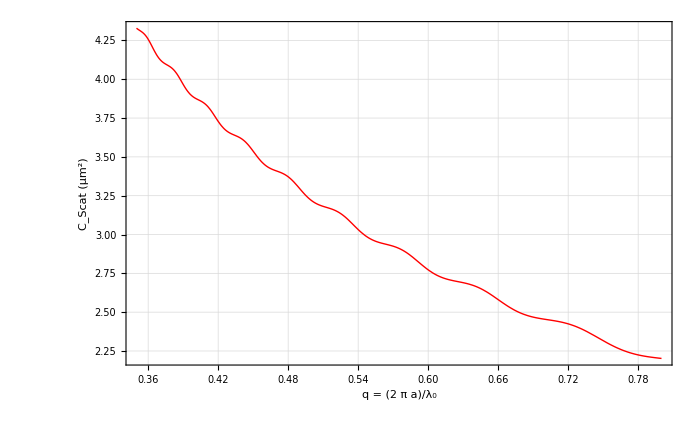

```mathematica
CScatPlot = Plot[CScat[.05* (2*Pi)/Subscript[λ, 0]], {Subscript[λ, 0],350*10^-3,800*10^-3},  PlotStyle-> RGBColor[1,0,0],FrameLabel-> {"q = (2  π a)/λ_0 for r=.05 microns", "C_Scat  (μm^2)"} ]
```

```mathematica
So by decreasing the wavelegnth (bluer)for a given particle size, we increase the size paramater and therefore increase the scattering crossection.
```

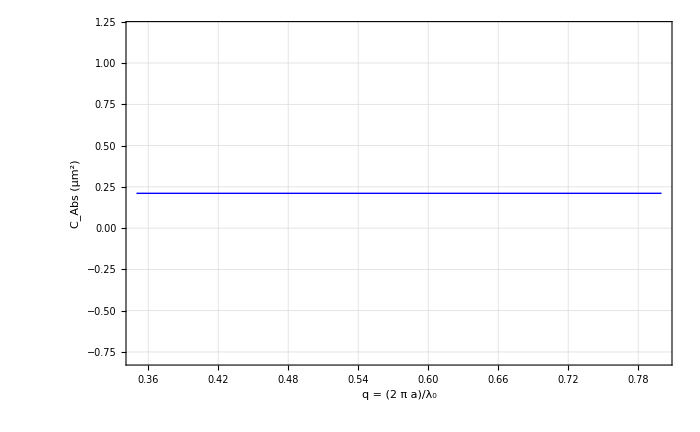

```mathematica
CAbsPlot = Plot[CAbs[.05* (2*Pi)/Subscript[λ, 0]], {i, 350*10^-3, 800*10^-3}, PlotStyle-> RGBColor[0,0,1],FrameLabel-> {"q = (2  π a)/λ_0", "C_Abs  (μm^2)"}]
```

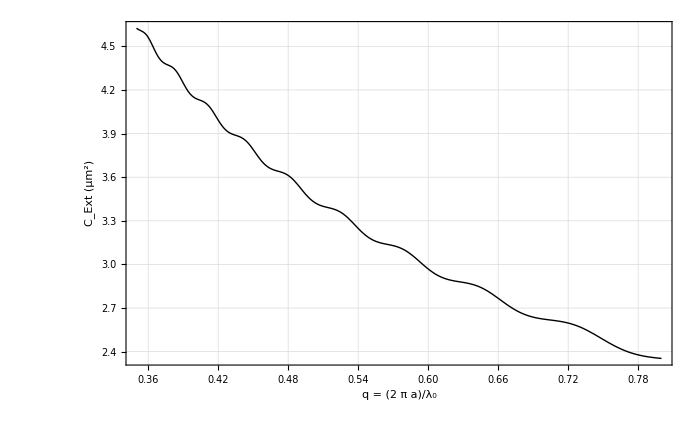

```mathematica
CExtPlot = Plot[CExt[.05* (2*Pi)/Subscript[λ, 0]], {Subscript[λ, 0],350*10^-3,800*10^-3}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0for r=.05 microns", "C_Ext  (μm^2)"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
Plot[{CExt[.05* (2*Pi)/Subscript[λ, 0]]CAbs[.05* Subscript[λ, 0]/(2π)],CScat[.05* (2*Pi)/Subscript[λ, 0]]}, {Subscript[λ, 0], 350*10^-3,800*10^-3}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0", "C_Ext  (μm^2)"}]
```

$Aborted

```mathematica
(* CLegend = {{{RGBColor[1,0,0],"C_scat"},{RGBColor[0,0,1],"C_abs"},{RGBColor[0,0,0],"C_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
(* ShowLegend[Show[CScatPlot,CAbsPlot,CExtPlot, DisplayFunction-> Identity], CLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the efficiencies

The efficiencies are defined simply as the ratio of the cross sections to the geometrical cross sectional area of the scatterer.

```mathematica
QScat[a_]:=  CScat[a]/(π a^2)
QAbs[a_]:= CAbs[a]/(π a^2)
QExt[a_]:=CExt[a]/(π a^2)
```

Print out efficiencies for the default parameters.

```mathematica
Print["Q_Scat = ",QScat[r]//N,"\nQ_Abs = ",QAbs[r]//N,"\nQ_Ext = ",QExt[r]//N ]
```

Q_Scat = 4.02511
Q_Abs = 0.372242
Q_Ext = 4.39736

#### Linear plots of size parameter vs. efficiency.

Note that these plots take longer to generate as the size parameter increases.  The multiplicative factor in the argument converts the abscissa variable to q values (rather than radius values).

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

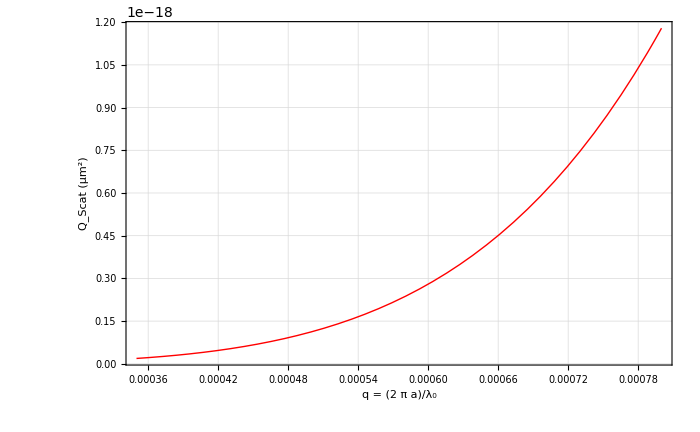

```mathematica
QScatPlot = Plot[QScat[.05* Subscript[λ, 0]/(2π)], {Subscript[λ, 0],350*10^-3,800*10^-3}, PlotStyle-> RGBColor[1,0,0],  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat  (μm^2)"}]
```

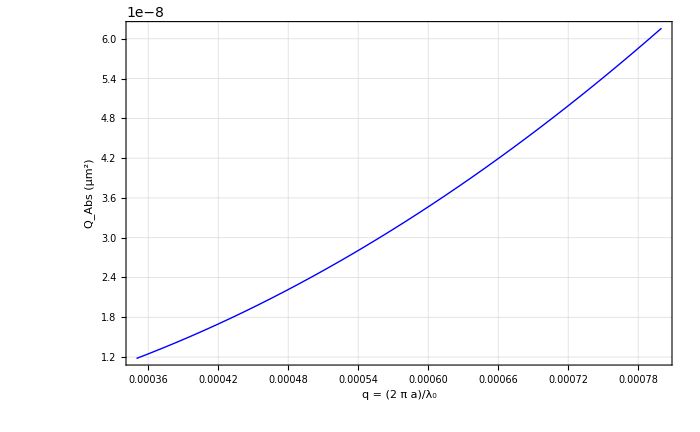

```mathematica
QAbsPlot = Plot[QAbs[.05* Subscript[λ, 0]/(2π)], {Subscript[λ, 0],350*10^-3,800*10^-3}, PlotStyle-> RGBColor[0,0,1], FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs  (μm^2)"}]
```

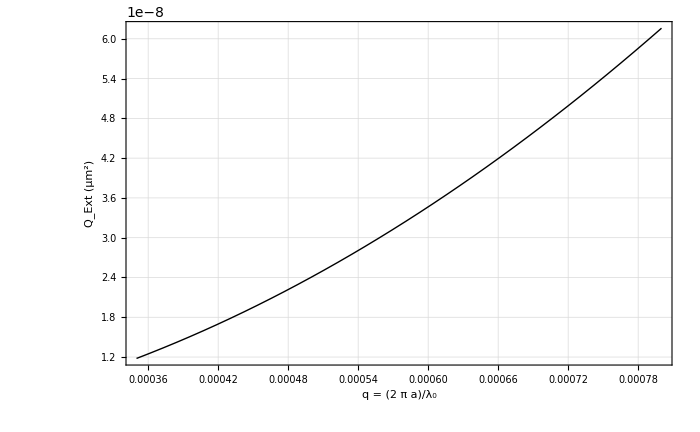

```mathematica
QExtPlot =Plot[QExt[.05* Subscript[λ, 0]/(2π)], {Subscript[λ, 0],350*10^-3,800*10^-3}, PlotStyle-> RGBColor[0,0,0], FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext  (μm^2)"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
(* QLegend = {{{RGBColor[1,0,0],"Q_scat"},{RGBColor[0,0,1],"Q_abs"},{RGBColor[0,0,0],"Q_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
(* ShowLegend[Show[QScatPlot,QAbsPlot,QExtPlot, PlotRange-> All,DisplayFunction-> Identity], QLegend,DisplayFunction-> $DisplayFunction ];
```

#### Log-linear plots of size parameter vs. efficiency.

These plots are useful when plotting over a large range of q values, but take longer to generate as the size parameter increases.  The multiplicative factor in the argument converts the abscissa variable to q values (rather than radius values).

```mathematica
(* SetOptions[LogLinearPlot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
Note from Guy: These scattering efficiencies should be dimensionless but were not coded so by Art Lampado.  I will go through and alter this.
```

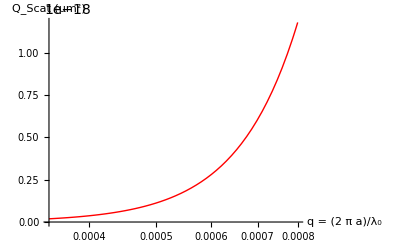

```mathematica
QScatLogPlot = LogLinearPlot[QScat[.05*Subscript[λ, 0]/(2π)], {Subscript[λ, 0],350*10^-3,800*10^-3}, PlotStyle-> RGBColor[1,0,0],  AxesLabel-> {"q = (2  π a)/λ_0", "Q_Scat  (μm^2)"}]
```

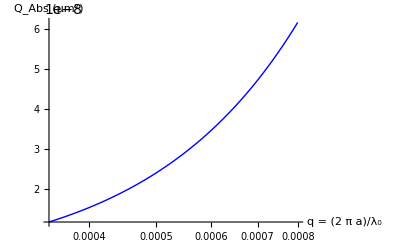

```mathematica
QAbsLogPlot = LogLinearPlot[QAbs[.05* Subscript[λ, 0]/(2π)], {Subscript[λ, 0],350*10^-6,800*10^-6}, PlotStyle-> RGBColor[0,0,1], AxesLabel-> {"q = (2  π a)/λ_0", "Q_Abs  (μm^2)"}]
```

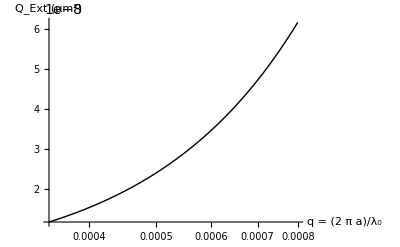

```mathematica
QExtLogPlot = LogLinearPlot[QExt[.05* Subscript[λ, 0]/(2π)], {Subscript[λ, 0],350*10^-3,800*10^-3}, PlotStyle-> RGBColor[0,0,0], AxesLabel-> {"q = (2  π a)/λ_0", "Q_Ext  (μm^2)"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
QLegend = {{{RGBColor[1,0,0],"Q_scat"},{RGBColor[0,0,1],"Q_abs"},{RGBColor[0,0,0],"Q_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
ShowLegend[Show[QScatLogPlot,QAbsLogPlot,QExtLogPlot, PlotRange-> All,DisplayFunction-> Identity], QLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the asymmetry factor

The equation for the asymmetry factor comes from Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001, pp. 1354-1361).

```mathematica
g[a_] := (2∑_(l=1)^LastTerm[a] ((l(l+2))/(l + 1) Re[(an[l,a]*  SuperStar[an[l+1,a]]+ bn[l,a]*SuperStar[bn[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(an[l,a] *SuperStar[bn[l,a]])]))/(∑_(l=1)^LastTerm[a] (2l+1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2))
```

```mathematica
StringJoin["The anisotropy value is g = ", ToString[-g[r]//N]]
```

The anisotropy value is g = -0.369377

#### Create plot of size parameter vs. asymmetry factor.

```mathematica
The assummetry factor denotes the symmetry of the phase function and related whether forward scattering or back scattering is dominant (greater than 1 is forward, less than 1 is backscattering).
```

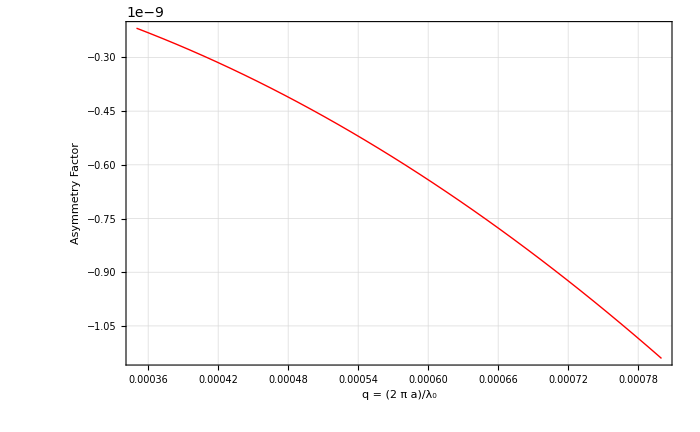

```mathematica
gPlot = Plot[g[.05 Subscript[λ, 0]/(2π)], {Subscript[λ, 0],350*10^-3,800*10^-3}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle-> RGBColor[1,0,0], GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Asymmetry Factor"}]
```

## Calculate and plot the albedo

The albedo is simply the ratio of the scattering to extinction cross sections.

```mathematica
albedo[a_] := CScat[a]/CExt[a];
StringJoin["The albedo is ", ToString[albedo[r]//N]]
```

The albedo is 0.915349

```mathematica
albedo[r]
```

0.915349

```mathematica
Manipulate[N[albedo[i*Subscript[λ, 0]/(2π)],3],{i,1,6}]
```

#### Create plot of albedo vs. size parameter.

```mathematica
(* SetOptions[LogLinearPlot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
(* In the next section of code, i is the size paramater.  *)
```

```mathematica
AlbedoPlot = LogLinearPlot[albedo[.05 Subscript[λ, 0]/(2π)], {Subscript[λ, 0],350*10^-3,800*10^-3}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle-> RGBColor[1,0,0], GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Albedo"}]
```

$Aborted

## Calculate and plot the scattering phase functions

Next, we construct the formulae for intensity as a function of angular position for incident radiation polarized in either of the two linear orthogonal polarization states.  Begin by defining the amplitude matrix elements, S1(r, θ) and S2(r, θ) which simplify the form of the resulting phase function equations a little

```mathematica
S1[a_,θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]pi[l,θ]+bn[l,a]  τ[l,θ]);
S2[a_,θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a] τ[l,θ]+bn[l,a]  pi[l,θ] );
```

```mathematica
(* Added by Guy *)
```

```mathematica
(* Look at the phase difference between the scattered beams A and B
```

```mathematica
(* N[(Re[S1[a,θ]]Im[S2[a,θ]]-Re[S2[a,θ]]Im[S1[a, θ]])/(Re[S1[a,θ]]Re[S2[a,θ]]+Im[S1[a,θ]]Im[S2[a, θ]]),3]
```

```mathematica
(*  θ1=ContourPlot[N[(Re[S1[a, θ]]Im[S2[a, θ]]-Re[S2[a, θ]]Im[S1[a, θ]])/(Re[S1[a, θ]]Re[S2[a, θ]]+Im[S1[a, θ]]Im[S2[a, θ]]),3],{a,0,1},{θ,0,.9π}]
```

```mathematica
Look at the scattering amplitude in the forward direction:
```

```mathematica
Cextfor=(Subscript[λ, 0]^2/Pi)*Re[S[1,0]]
```

(296527078849 Re[S[1,0]])/(1000000000000 π)

Here are the phase function equations.  The normalization factor (to insure ∫P(cos(θ))ⅆΩ =  1) is sometime used in the literature (e.g., Fu and Sun) and sometimes neglected (e.g Bohren and Huffman).  Therefore, two separate functions for the unpolarized scattering phase function are created and either one may be used.

```mathematica
Iperp[a_, θ_]:= (Abs[S1[a,θ]])^2;

Ipar[a_, θ_]:= (Abs[S2[a,θ]])^2;

Iunpol[a_, θ_]:= (Iperp[a, θ] + Ipar[a, θ])/2;

Norma[a_]:=∑_(l=1)^LastTerm[a] 2(l + 1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2)

IunpolNorm[a_, θ_]:= (Iperp[a, θ] + Ipar[a, θ])/Norma[a];
```

### Create plots of the phase functions.

#### Log-linear plots of scattered intensity vs. angle.

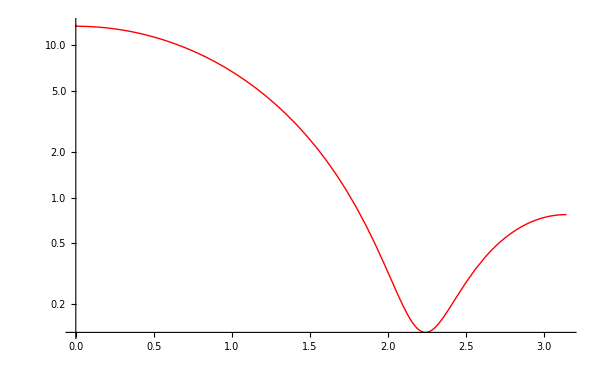

```mathematica
IPerpPlot = LogPlot[Evaluate[Iperp[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[1,0,0],  FrameLabel-> {"θ (deg)", "I_perp Phase Function"}]
```

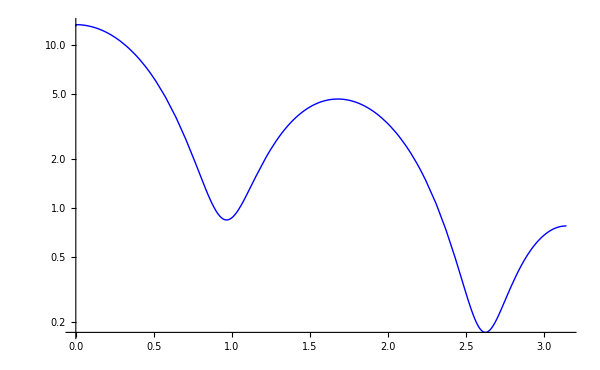

```mathematica
IParPlot = LogPlot[Evaluate[Ipar[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[0,0,1],  FrameLabel-> {"θ (deg)", "I_par Phase Function"}]
```

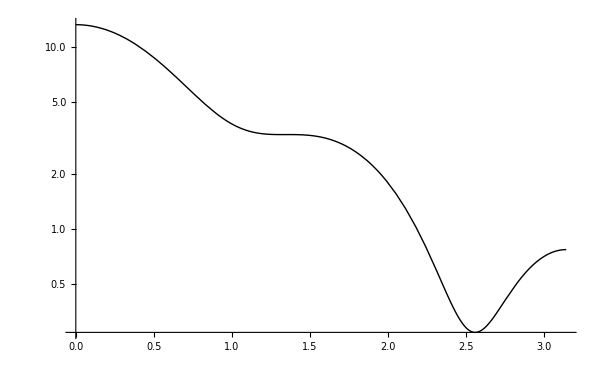

```mathematica
IUnpolPlot = LogPlot[Evaluate[Iunpol[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[0,0,0],  FrameLabel-> {"θ (deg)", "I_unpol Phase Function"}]
```

All three on the same plot.  The first expression creates a legend for the plot.

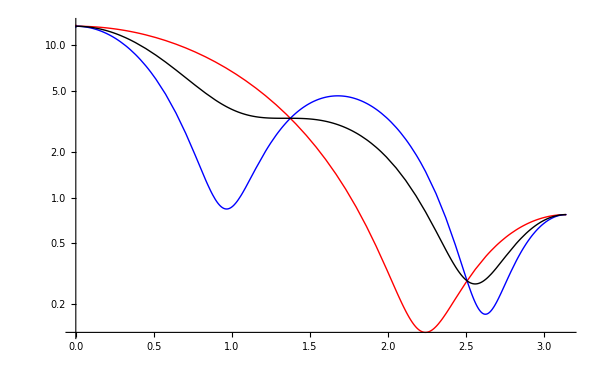

```mathematica
ILegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.5,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
Show[IPerpPlot,IParPlot,IUnpolPlot, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{"θ (deg)", "Phase Functions"} ]
```

#### Polar plots of scattered intensity vs. angle.

Begin by defining some additional graphics to make the polar plots look good.  Note that when we normalize the phase functions to the peak value (which is the same for all polarization states), the maximum corresponds to θ = 0.   The PlotMax variable in the next cell permits the user to change the plot range, permitting "zooming" to look at the fine structure close to the particle.

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
MyRings = Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},i]},{i,0,1,0.1}]];
NormFactor = NLimit[Iperp[r,ϕ], ϕ-> 0.01, WorkingPrecision-> 20,Terms->6];
```

```mathematica
N[NormFactor,3]
```

13.2993

```mathematica
PlotMax = 1.025;
```

```mathematica
SetOptions[PolarPlot, Frame-> True, PlotRange-> All, ImageSize-> 500,  PlotPoints->30,  AspectRatio-> 1, FrameTicks-> None,PlotRange-> {{-PlotMax,PlotMax}, {-PlotMax,PlotMax}}, DisplayFunction-> Identity ];
```

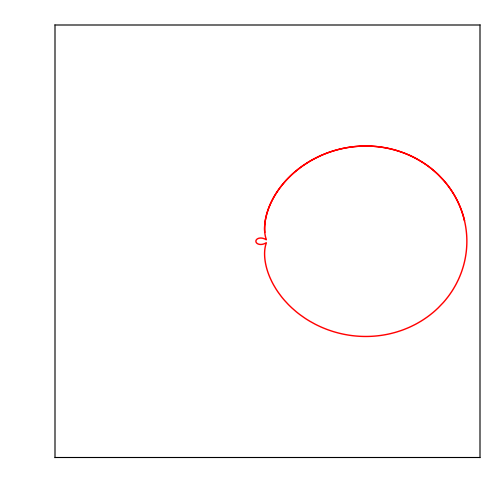

```mathematica
IPolarPerp = PolarPlot[Evaluate[Iperp[r,θ]/NormFactor], {θ,.1,2.6*Pi},PlotStyle-> RGBColor[1,0,0]]
```

I_parvs. θ

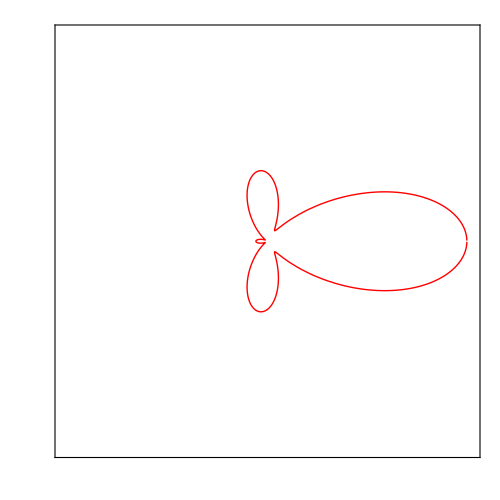

```mathematica
IPolarPar = PolarPlot[Evaluate[Ipar[r,θ]/NormFactor], {θ, π*.001,1.999π},PlotStyle-> RGBColor[1,0,0]]
```

I_unpolvs. θ

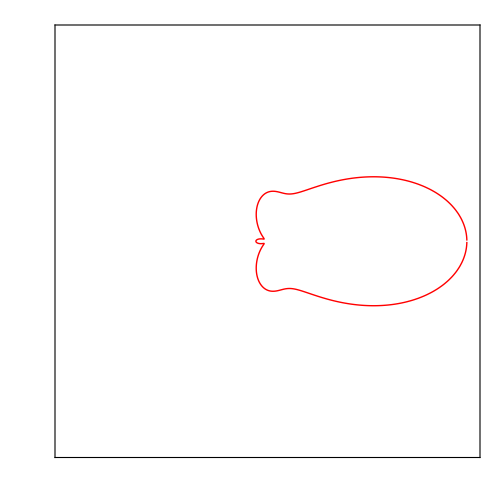

```mathematica
IPolarUnpol = PolarPlot[Evaluate[Iunpol[r,θ]/NormFactor], {θ, π*.001,1.999π},PlotStyle-> RGBColor[1,0,0]]
```

All three on the same plot.  The first expression creates a legend for the plot.

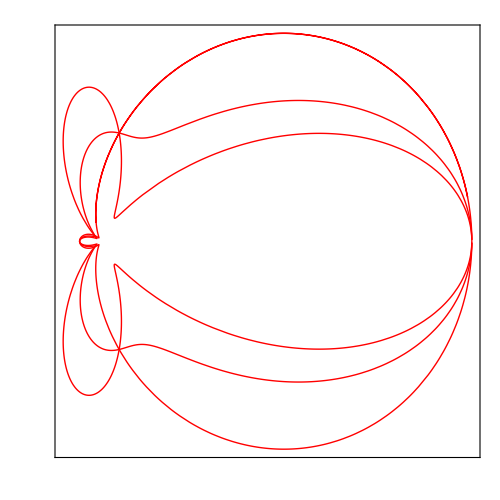

```mathematica
IPolarLegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.63,.6}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
Show[IPolarPerp,IPolarPar,IPolarUnpol, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{None,None,"Normalized Phase Functions", None} ]
```

#### Log-polar plots of scattered intensity vs. angle.

Begin by defining a few labels and some additional graphics to make the polar plots look good.  Note that I normalize the phase functions to the peak value (which is the same for all polarization states and occurs in the forward direction where θ = 0).

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
LogRings = Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},Log[10,i]]},{i,1.105171,10,1.1105171}]];
LogNormFactor = NLimit[Log[10,Iperp[r, ϕ]], ϕ-> 0.0, WorkingPrecision-> 20, Terms ->  6];
```

```mathematica
SetOptions[PolarPlot, Frame-> True, PlotRange-> All, ImageSize-> 500,  PlotPoints->30,  AspectRatio-> 1, FrameTicks-> None, Ticks-> None, DisplayFunction-> Identity ];
```

```mathematica
PerpMinValue = FindMinimum[Iperp[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
ParMinValue = FindMinimum[Ipar[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
UnpolMinValue = FindMinimum[Iunpol[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
```

I_perpvs. θ

```mathematica
Timing[ILogPolarPerp = PolarPlot[Evaluate[Log[10,Iperp[r, θ]  + (1-Iperp[r, PerpMinValue])]/LogNormFactor], {θ, 0, 2π}, PlotStyle-> RGBColor[1,0,0], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 2.2401 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.421,Null}

```mathematica
Show[ILogPolarPerp, MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

I_parvs. θ

```mathematica
Timing[ILogPolarPar = PolarPlot[Evaluate[Log[10,Ipar[r, θ]  + (1-Ipar[r, ParMinValue])]/LogNormFactor], {θ, 0, 2π},  PlotStyle-> RGBColor[0,0,1], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 2.62399 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.39,Null}

```mathematica
Show[ILogPolarPar,  MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

I_unpolvs. θ

```mathematica
Timing[ILogPolarUnPol = PolarPlot[Evaluate[Log[10,Iunpol[r, θ]  + (1-Iunpol[r, UnpolMinValue])]/LogNormFactor], {θ, 0, 2π}, PlotStyle-> RGBColor[0,0,0], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 2.55851 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.515,Null}

```mathematica
Show[ILogPolarUnPol, MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

All three on the same plot.  The first expression creates a legend for the plot.

```mathematica
ILogPolarLegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.63,.6}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
ShowLegend[Show[ILogPolarPerp,ILogPolarPar,ILogPolarUnPol,MySpokes, LogRings, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{None,None,"Log Phase Functions", None} ], ILogPolarLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the polarization ratio for unpolarized incident light

Note that this definition applies to an unpolarized incident beam.

```mathematica
PolRatio[a_, θ_]:=(Iperp[a, θ] - Ipar[a, θ])/(Iperp[a, θ] + Ipar[a, θ]);
```

Plot of the polarization ratio vs. angle

```mathematica
PolRatioPlot = Plot[Evaluate[PolRatio[r, θ]], {θ, 0, π}, Frame-> True, PlotRange-> {-1,1}, ImageSize-> 700, PlotStyle-> RGBColor[0,0,0], GridLines-> Automatic, FrameLabel-> {"θ (rad)","Polarization Ratio", "Polarization Ratio = I_perp/I_perp", None}]
```

-Graphics-

## 3-D Plots

Here are some 3 dimensional plots of the phase functions.   These plots are handy because they reveal the asymmetry of the surfaces when a completely polarized input plane wave is incident.  The unpolarized case degenerates into a symmetric surface (about the optical axis).  This first few cells contain the amplitude matrix and intensity functions and were actually defined earlier for the 2D plots.  They are included here in case the cells for the 2D plots have not been evaluated.  Also included are the two possible normalizing factors for the unpolarized case (see above).

```mathematica
S1[a_, θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]*pi[l,θ]+bn[l,a]*τ[l,θ])
S2[a_, θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l, a]*τ[l,θ]+bn[l,a]*pi[l,θ] )
```

```mathematica
S1[a_,θ_]:=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]*pi[l,θ]+bn[l,a]* τ[l,θ1]))/.θ1-> θ;
S2[a_,θ_] :=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a]* τ[l,θ1]+bn[l,a]*pi[l,θ] ))/.θ1-> θ;
AmpMatrix[a_,θ_]:={{S2[a,θ],0},{0,S1[a,θ]}}
```

These are the 3D extensions of the intensity functions.  The ϕ dependence is on sin^2(ϕ) for the perpendicular case and on cos^2(ϕ) for the parallel case.

```mathematica
Iperp3D[a_,θ_,ϕ_]:= (Abs[S1[a,θ]] Sin[ϕ])^2
Ipar3D[a_,θ_,ϕ_]:= (Abs[S2[a,θ]] Cos[ϕ])^2
Iunpol3D[a_,θ_,ϕ_]:= (Iperp3D[a,θ,ϕ] + Ipar3D[a,θ,ϕ])/2
Norma2[a_]:=∑_(l=1)^LastTerm[a] 2(l + 1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2)
IunpolNorm3D[a_, θ_, ϕ_]:= (Iperp3D[a, θ, ϕ] + Ipar3D[a, θ, ϕ])/Norma2[a]
```

```mathematica
By integrating the scattering function for the unpolarized case, I can determine the total amount of scattered light within a certain angular region with respect to the particle.  Of particular region is the fraction of the scattered light that is inside the exit code.  This assumes that the light is normal to the interface and approaching a particle.
```

```mathematica
This can then be modified to deal with light approaching the particle from an angle and therefor the criticale angles will change.
```

```mathematica
NIntegrate[NIntegrate[IunpolNorm3D[r,θ,ϕ],{ θ,0,2Pi}],{ ϕ,0,Pi/20}]
```

NIntegrate::inumr: The integrand 0.120579\ (Abs[3/2\ Plus[« 2 »] + 5/6\ Plus[« 2 »] + 7/12\ Plus[« 2 »] + 9/20\ Plus[« 2 »] + « 5 » + 21/110\ Plus[« 2 »] + 23/132\ Plus[« 2 »] + 25/156\ Plus[« 2 »] + 27/182\ Plus[« 2 »]]^2\ Cos[ϕ]^2 + Abs[3/2\ Plus[« 2 »] + 5/6\ Plus[« 2 »] + « 9 » + 25/156\ Plus[« 2 »] + 27/182\ Plus[« 2 »]]^2\ Sin[ϕ]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

0.417348

```mathematica
NIntegrate[NIntegrate[IunpolNorm3D[r,θ,ϕ],{ θ,0,2Pi}],{ ϕ,0,π/2}]
```

NIntegrate::inumr: The integrand 0.120579\ (Abs[3/2\ Plus[« 2 »] + 5/6\ Plus[« 2 »] + 7/12\ Plus[« 2 »] + 9/20\ Plus[« 2 »] + « 5 » + 21/110\ Plus[« 2 »] + 23/132\ Plus[« 2 »] + 25/156\ Plus[« 2 »] + 27/182\ Plus[« 2 »]]^2\ Cos[ϕ]^2 + Abs[3/2\ Plus[« 2 »] + 5/6\ Plus[« 2 »] + « 9 » + 25/156\ Plus[« 2 »] + 27/182\ Plus[« 2 »]]^2\ Sin[ϕ]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

4.75519

Values required to center the particle at the origin.  Note there is no need to consider the ϕ dimension here so I use the 2D equations which evaluate more quickly.

```mathematica
Needs["NumericalCalculus'"]
```

Context::quote: Warning: "NumericalCalculus'" is not a valid context. A valid context uses back quotes instead of forward quotes as in "NumericalCalculus`".

Needs::cxt: Invalid context specified at position 1 in Needs["NumericalCalculus'"]. A context must consist of valid symbol names separated by and ending with "`".

Needs[NumericalCalculus']

```mathematica
NormFactor = NLimit[Iperp[r, ϕ], ϕ-> 0.01, WorkingPrecision-> 20, Terms ->  6]
LogNormFactor = NLimit[Log[10,Iperp[r, ϕ]], ϕ-> 0.01, WorkingPrecision-> 20, Terms ->  6]
```

13.2993

1.12383

```mathematica
PerpMinValue = FindMinimum[(Abs[S1[r,θ]])^2/NormFactor, {θ,  0.01,π}]
ParMinValue = FindMinimum[(Abs[S2[r,θ]])^2/NormFactor, {θ,  0.01,π}]
UnpolMinValue = FindMinimum[(Iperp[r, θ] + Ipar[r, θ])/(2 NormFactor), {θ,  0.01,π}]
```

{0.0098125,{θ→2.2401}}

{0.0632796,{θ→0.966113}}

{0.0204025,{θ→3.72468}}

```mathematica
Abort[]
```

```mathematica
PerpMinValue=.0098125;
ParMinValue=.06;
UnpolMinValue=.0195209;
```

#### Plot the phase functions.

Start out by setting up the graphics.

```mathematica
SetOptions[SphericalPlot3D,BoxRatios->{1,1,1}, AspectRatio->1, Axes->True, PlotPoints->40,ViewPoint->{-15,0,0}, Boxed->False,ViewVertical->{0,1,0}, PlotRange-> All , LightSources->{{{1,0,1}, RGBColor[1,0,0]}, {{1,1,1},RGBColor[0,1,0]},{{0,1,1},RGBColor[0,0,1]},{{-1,0,-1},RGBColor[1,0,0]},{{-1,-1,-1},RGBColor[0,1,0]},{{0,-1,-1} ,RGBColor[0,0,1] }}];
```

SetOptions::optnf: LightSources is not a known option for SphericalPlot3D.

These next few cells can take long when the sampling is fine (i.e., when the PlotPoints value is set high).  Have patience.  Also, these plots will crash for angular values of exactly nπ (n = 0, ±1, ±2, ...).  I get around this by choosing plot ranges that only approach these values, rather than redefining the functions as their limiting values for all of these possible cases.  The latter approach, although more thorough, tends to extend the computation time substantially and adequate approximations can be made using the former by adding more digits (zeros or nines) to the arguments.  There are two plots for each phase function, a side view and an end view, and these are helpful in examining the asymmetry of the surfaces.  Start with the perpendicular phase function.

```mathematica
FullSimplify[S1[r,θ]]
```

(1.+0. ⅈ) ((-0.660901+0.246037 ⅈ)-(0.55264-0.0499857 ⅈ) Cos[θ]+(0.651527-0.25192 ⅈ) Cos[2 θ]+(0.552332-0.0525171 ⅈ) Cos[3 θ]+(0.00936132+0.00574923 ⅈ) Cos[4 θ]+(0.000308238+0.0025275 ⅈ) Cos[5 θ]+(0.0000129618+0.0001338 ⅈ) Cos[6 θ]+(3.62306×10^-7+3.86199×10^-6 ⅈ) Cos[7 θ]+(6.91748×10^-9+7.39744×10^-8 ⅈ) Cos[8 θ]+(9.62009×10^-11+1.02559×10^-9 ⅈ) Cos[9 θ]+(1.02154×10^-12+1.08451×10^-11 ⅈ) Cos[10 θ]+(8.57573×10^-15+9.06898×10^-14 ⅈ) Cos[11 θ]+(5.84453×10^-17+6.16053×10^-16 ⅈ) Cos[12 θ]+(3.30206×10^-19+3.47142×10^-18 ⅈ) Cos[13 θ]+(1.57309×10^-21+1.65031×10^-20 ⅈ) Cos[14 θ]+(6.30284×10^-24+6.96176×10^-23 ⅈ) Cos[15 θ]) Csc[θ]^3 √(Sin[θ]^2)

```mathematica
FullSimplify[S2[r,θ]]
```

(1.+0. ⅈ) ((0.360739-0.453467 ⅈ)-(0.329732-0.0110664 ⅈ) Cos[θ]-(0.849592-0.630711 ⅈ) Cos[2 θ]+(0.322332+0.0402188 ⅈ) Cos[3 θ]+(0.488715-0.174935 ⅈ) Cos[4 θ]+(0.00739654-0.0512113 ⅈ) Cos[5 θ]+(0.000138716-0.00230769 ⅈ) Cos[6 θ]+(3.77617×10^-6-0.0000739027 ⅈ) Cos[7 θ]+(7.96941×10^-8-1.6645×10^-6 ⅈ) Cos[8 θ]+(1.26315×10^-9-2.74296×10^-8 ⅈ) Cos[9 θ]+(1.54226×10^-11-3.43759×10^-10 ⅈ) Cos[10 θ]+(1.48922×10^-13-3.38181×10^-12 ⅈ) Cos[11 θ]+(1.16353×10^-15-2.67931×10^-14 ⅈ) Cos[12 θ]+(7.49909×10^-18-1.74561×10^-16 ⅈ) Cos[13 θ]+(4.05295×10^-20-9.51584×10^-19 ⅈ) Cos[14 θ]+(1.86242×10^-22-4.40361×10^-21 ⅈ) Cos[15 θ]) Csc[θ]^3 √(Sin[θ]^2)

```mathematica
FullSimplify[Iperp3D[r,b,c]]
```

2. Abs[((-0.420071+0.307497 ⅈ)-(0.501647+0.191338 ⅈ) Cos[b]+(0.193797-0.261305 ⅈ) Cos[2 b]+(0.499166+0.189769 ⅈ) Cos[3 b]+(0.226182-0.0467096 ⅈ) Cos[4 b]+(0.00247735+0.00154069 ⅈ) Cos[5 b]+(0.0000920156+0.000517036 ⅈ) Cos[6 b]+(3.61596×10^-6+0.0000290355 ⅈ) Cos[7 b]+(1.06072×10^-7+9.6727×10^-7 ⅈ) Cos[8 b]+(2.32464×10^-9+2.25223×10^-8 ⅈ) Cos[9 b]+(3.92899×10^-11+3.93747×10^-10 ⅈ) Cos[10 b]+(5.27339×10^-13+5.39728×10^-12 ⅈ) Cos[11 b]+(5.75854×10^-15+5.97857×10^-14 ⅈ) Cos[12 b]+(5.21889×10^-17+5.47453×10^-16 ⅈ) Cos[13 b]+(3.99065×10^-19+4.21921×10^-18 ⅈ) Cos[14 b]+(2.46354×10^-21+2.97811×10^-20 ⅈ) Cos[15 b]) Csc[b]^2]^2 Sin[c]^2

```mathematica
(* Simplify[Evaluate[Log[10,Iperp3D[r,θ,ϕ] +(1-Iperp3D[r,PerpMinValue,ϕ])]/LogNormFactor]]
```

General::ivar: 0.022296 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

{0.279657 Log[1-(Abs[27/182 ((-1.05976×10^-17+1.4457×10^-16 ⅈ)+(1.79327×10^-21+2.16785×10^-20 ⅈ) ∂_{0.022296,{θ→1.63722}} {-2.00616,{(91. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12))/(-1.+Cos[θ→1.63722])}})+25/156 ((-1.29249×10^-15+1.74438×10^-14 ⅈ)+(2.84531×10^-19+3.46659×10^-18 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.72236,{(78. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11))/(-1.+Cos[θ→1.63722])}})+23/132 ((-1.33009×10^-13+1.77133×10^-12 ⅈ)+(3.87067×10^-17+4.76186×10^-16 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.45956,{(66. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10))/(-1.+Cos[θ→1.63722])}})+21/110 ((-1.13803×10^-11+1.49001×10^-10 ⅈ)+(4.45321×10^-15+5.54629×10^-14 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.21797,{(55. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9))/(-1.+Cos[θ→1.63722])}})+19/90 ((-7.95823×10^-10+1.0189×10^-8 ⅈ)+(4.26174×10^-13+5.39275×10^-12 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.997763,{(45. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8))/(-1.+Cos[θ→1.63722])}})+17/72 ((-4.45991×10^-8+5.53776×10^-7 ⅈ)+(3.32336×10^-11+4.29462×10^-10 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.799105,{(36. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7))/(-1.+Cos[θ→1.63722])}})+15/56 ((-1.96012×10^-6+0.0000232821 ⅈ)+(2.05662×10^-9+2.73493×10^-8 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.622145,{(28. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6))/(-1.+Cos[θ→1.63722])}})+13/42 ((-0.0000662473+0.000733664 ⅈ)+(9.74738×10^-8+1.34993×10^-6 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.467015,{(21. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5))/(-1.+Cos[θ→1.63722])}})+11/30 ((-0.00174063+0.0168208 ⅈ)+(3.36367×10^-6+0.0000494682 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.333831,{(15. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4))/(-1.+Cos[θ→1.63722])}})+9/20 ((-0.0476858+0.285054 ⅈ)+(0.0000791525+0.00126049 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.222693,{(10. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3))/(-1.+Cos[θ→1.63722])}})+7/12 ((-3.28675+1.79708 ⅈ)+(0.00141594+0.0198896 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.133682,{(6. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+5/6 ((-2.69417-0.538612 ⅈ)+(0.0324621+0.15969 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.066866,{(3. (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+3/2 ((-0.739217+0.40274 ⅈ)+(0.395794+0.473621 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.0222942,{(1. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})])^2 Sin[ϕ]^2+(Abs[3/2 ((-0.739217+0.40274 ⅈ) √(1-Cos[θ]^2) Csc[θ]-((0.395794+0.473621 ⅈ) Cos[θ] Sin[θ])/(√(1-Cos[θ]^2)))+5/6 ((-2.69484-0.538746 ⅈ) √(1-Cos[θ]^2) Cot[θ]+(0.0324621+0.15969 ⅈ) (-(3 Cos[θ]^2 Sin[θ])/(√(1-Cos[θ]^2))+3 √(1-Cos[θ]^2) Sin[θ]))+7/12 ((-0.822199+0.449549 ⅈ) √(1-Cos[θ]^2) (-1+5 Cos[θ]^2) Csc[θ]+(0.00141594+0.0198896 ⅈ) (15 Cos[θ] √(1-Cos[θ]^2) Sin[θ]-(3 Cos[θ] (-1+5 Cos[θ]^2) Sin[θ])/(2 √(1-Cos[θ]^2))))+9/20 ((-0.0119348+0.0713433 ⅈ) √(1-Cos[θ]^2) (-3 Cos[θ]+7 Cos[θ]^3) Csc[θ]+(0.0000791525+0.00126049 ⅈ) (-(5 Cos[θ] (-3 Cos[θ]+7 Cos[θ]^3) Sin[θ])/(2 √(1-Cos[θ]^2))-5/2 √(1-Cos[θ]^2) (3 Sin[θ]-21 Cos[θ]^2 Sin[θ])))+11/30 ((-0.000217958+0.00210626 ⅈ) √(1-Cos[θ]^2) (1-14 Cos[θ]^2+21 Cos[θ]^4) Csc[θ]+(3.36367×10^-6+0.0000494682 ⅈ) (-(15 Cos[θ] (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(8 √(1-Cos[θ]^2))-15/8 √(1-Cos[θ]^2) (28 Cos[θ] Sin[θ]-84 Cos[θ]^3 Sin[θ])))+13/42 ((-8.30153×10^-6+0.0000919363 ⅈ) √(1-Cos[θ]^2) (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Csc[θ]+(9.74738×10^-8+1.34993×10^-6 ⅈ) (-(21 Cos[θ] (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Sin[θ])/(8 √(1-Cos[θ]^2))-21/8 √(1-Cos[θ]^2) (-5 Sin[θ]+90 Cos[θ]^2 Sin[θ]-165 Cos[θ]^4 Sin[θ])))+15/56 ((-3.07298×10^-8+3.65006×10^-7 ⅈ) √(1-Cos[θ]^2) (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Csc[θ]+(2.05662×10^-9+2.73493×10^-8 ⅈ) (-(7 Cos[θ] (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Sin[θ])/(16 √(1-Cos[θ]^2))-7/16 √(1-Cos[θ]^2) (-270 Cos[θ] Sin[θ]+1980 Cos[θ]^3 Sin[θ]-2574 Cos[θ]^5 Sin[θ])))+17/72 ((-6.99902×10^-10+8.6905×10^-9 ⅈ) √(1-Cos[θ]^2) (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Csc[θ]+(3.32336×10^-11+4.29462×10^-10 ⅈ) (-(9 Cos[θ] (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Sin[θ])/(16 √(1-Cos[θ]^2))-9/16 √(1-Cos[θ]^2) (35 Sin[θ]-1155 Cos[θ]^2 Sin[θ]+5005 Cos[θ]^4 Sin[θ]-5005 Cos[θ]^6 Sin[θ])))+19/90 ((-6.25149×10^-12+8.00387×10^-11 ⅈ) √(1-Cos[θ]^2) (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Csc[θ]+(4.26174×10^-13+5.39275×10^-12 ⅈ) (-1/(128 √(1-Cos[θ]^2))45 Cos[θ] (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Sin[θ]-45/128 √(1-Cos[θ]^2) (616 Cos[θ] Sin[θ]-8008 Cos[θ]^3 Sin[θ]+24024 Cos[θ]^5 Sin[θ]-19448 Cos[θ]^7 Sin[θ])))+21/110 ((-8.95082×10^-14+1.17191×10^-12 ⅈ) √(1-Cos[θ]^2) (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Csc[θ]+(4.45321×10^-15+5.54629×10^-14 ⅈ) (-1/(128 √(1-Cos[θ]^2))55 Cos[θ] (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Sin[θ]-55/128 √(1-Cos[θ]^2) (-63 Sin[θ]+3276 Cos[θ]^2 Sin[θ]-24570 Cos[θ]^4 Sin[θ]+55692 Cos[θ]^6 Sin[θ]-37791 Cos[θ]^8 Sin[θ])))+23/132 ((-2.61893×10^-16+3.48774×10^-15 ⅈ) √(1-Cos[θ]^2) (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Csc[θ]+(3.87067×10^-17+4.76186×10^-16 ⅈ) (-1/(256 √(1-Cos[θ]^2))33 Cos[θ] (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Sin[θ]-33/256 √(1-Cos[θ]^2) (-2730 Cos[θ] Sin[θ]+54600 Cos[θ]^3 Sin[θ]-278460 Cos[θ]^5 Sin[θ]+503880 Cos[θ]^7 Sin[θ]-293930 Cos[θ]^9 Sin[θ])))+25/156 ((-2.54871×10^-18+3.4398×10^-17 ⅈ) √(1-Cos[θ]^2) (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Csc[θ]+(2.84531×10^-19+3.46659×10^-18 ⅈ) (-1/(256 √(1-Cos[θ]^2))39 Cos[θ] (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Sin[θ]-39/256 √(1-Cos[θ]^2) (231 Sin[θ]-17325 Cos[θ]^2 Sin[θ]+196350 Cos[θ]^4 Sin[θ]-746130 Cos[θ]^6 Sin[θ]+1119195 Cos[θ]^8 Sin[θ]-572033 Cos[θ]^10 Sin[θ])))+27/182 ((-1.04658×10^-20+1.42773×10^-19 ⅈ) √(1-Cos[θ]^2) (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Csc[θ]+(1.79327×10^-21+2.16785×10^-20 ⅈ) (-(91 Cos[θ] (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Sin[θ])/(1024 √(1-Cos[θ]^2))-1/1024 91 √(1-Cos[θ]^2) (5940 Cos[θ] Sin[θ]-168300 Cos[θ]^3 Sin[θ]+1279080 Cos[θ]^5 Sin[θ]-3837240 Cos[θ]^7 Sin[θ]+4903140 Cos[θ]^9 Sin[θ]-2228700 Cos[θ]^11 Sin[θ])))])^2 Sin[ϕ]^2],{0.279657 Log[1-(Abs[27/182 (((1.0717×10^-17-1.46199×10^-16 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(1.79327×10^-21+2.16785×10^-20 ⅈ) ∂_{0.022296,{θ→1.63722}} {-2.00616,{(91. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12))/(-1.+Cos[θ→1.63722])}})+25/156 (((1.30494×10^-15-1.76118×10^-14 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(2.84531×10^-19+3.46659×10^-18 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.72236,{(78. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11))/(-1.+Cos[θ→1.63722])}})+23/132 (((1.34089×10^-13-1.78572×10^-12 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.87067×10^-17+4.76186×10^-16 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.45956,{(66. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10))/(-1.+Cos[θ→1.63722])}})+21/110 (((1.1457×10^-11-1.50005×10^-10 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(4.45321×10^-15+5.54629×10^-14 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.21797,{(55. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9))/(-1.+Cos[θ→1.63722])}})+19/90 (((8.0019×10^-10-1.0245×10^-8 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(4.26174×10^-13+5.39275×10^-12 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.997763,{(45. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8))/(-1.+Cos[θ→1.63722])}})+17/72 (((4.47937×10^-8-5.56192×10^-7 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.32336×10^-11+4.29462×10^-10 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.799105,{(36. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7))/(-1.+Cos[θ→1.63722])}})+15/56 (((1.96671×10^-6-0.0000233604 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(2.05662×10^-9+2.73493×10^-8 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.622145,{(28. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6))/(-1.+Cos[θ→1.63722])}})+13/42 (((0.0000664122-0.00073549 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(9.74738×10^-8+1.34993×10^-6 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.467015,{(21. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5))/(-1.+Cos[θ→1.63722])}})+11/30 (((0.00174367-0.0168501 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.36367×10^-6+0.0000494682 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.333831,{(15. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4))/(-1.+Cos[θ→1.63722])}})+9/20 (((0.0477392-0.285373 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.0000791525+0.00126049 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.222693,{(10. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3))/(-1.+Cos[θ→1.63722])}})+7/12 (((3.2888-1.7982 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.00141594+0.0198896 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.133682,{(6. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+5/6 (((2.69484+0.538746 ⅈ) (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.0324621+0.15969 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.066866,{(3. (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+3/2 (((0.739217-0.40274 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.395794+0.473621 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.0222942,{(1. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})])^2 Sin[ϕ]^2+(Abs[3/2 ((-0.739217+0.40274 ⅈ) √(1-Cos[θ]^2) Csc[θ]-((0.395794+0.473621 ⅈ) Cos[θ] Sin[θ])/(√(1-Cos[θ]^2)))+5/6 ((-2.69484-0.538746 ⅈ) √(1-Cos[θ]^2) Cot[θ]+(0.0324621+0.15969 ⅈ) (-(3 Cos[θ]^2 Sin[θ])/(√(1-Cos[θ]^2))+3 √(1-Cos[θ]^2) Sin[θ]))+7/12 ((-0.822199+0.449549 ⅈ) √(1-Cos[θ]^2) (-1+5 Cos[θ]^2) Csc[θ]+(0.00141594+0.0198896 ⅈ) (15 Cos[θ] √(1-Cos[θ]^2) Sin[θ]-(3 Cos[θ] (-1+5 Cos[θ]^2) Sin[θ])/(2 √(1-Cos[θ]^2))))+9/20 ((-0.0119348+0.0713433 ⅈ) √(1-Cos[θ]^2) (-3 Cos[θ]+7 Cos[θ]^3) Csc[θ]+(0.0000791525+0.00126049 ⅈ) (-(5 Cos[θ] (-3 Cos[θ]+7 Cos[θ]^3) Sin[θ])/(2 √(1-Cos[θ]^2))-5/2 √(1-Cos[θ]^2) (3 Sin[θ]-21 Cos[θ]^2 Sin[θ])))+11/30 ((-0.000217958+0.00210626 ⅈ) √(1-Cos[θ]^2) (1-14 Cos[θ]^2+21 Cos[θ]^4) Csc[θ]+(3.36367×10^-6+0.0000494682 ⅈ) (-(15 Cos[θ] (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(8 √(1-Cos[θ]^2))-15/8 √(1-Cos[θ]^2) (28 Cos[θ] Sin[θ]-84 Cos[θ]^3 Sin[θ])))+13/42 ((-8.30153×10^-6+0.0000919363 ⅈ) √(1-Cos[θ]^2) (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Csc[θ]+(9.74738×10^-8+1.34993×10^-6 ⅈ) (-(21 Cos[θ] (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Sin[θ])/(8 √(1-Cos[θ]^2))-21/8 √(1-Cos[θ]^2) (-5 Sin[θ]+90 Cos[θ]^2 Sin[θ]-165 Cos[θ]^4 Sin[θ])))+15/56 ((-3.07298×10^-8+3.65006×10^-7 ⅈ) √(1-Cos[θ]^2) (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Csc[θ]+(2.05662×10^-9+2.73493×10^-8 ⅈ) (-(7 Cos[θ] (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Sin[θ])/(16 √(1-Cos[θ]^2))-7/16 √(1-Cos[θ]^2) (-270 Cos[θ] Sin[θ]+1980 Cos[θ]^3 Sin[θ]-2574 Cos[θ]^5 Sin[θ])))+17/72 ((-6.99902×10^-10+8.6905×10^-9 ⅈ) √(1-Cos[θ]^2) (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Csc[θ]+(3.32336×10^-11+4.29462×10^-10 ⅈ) (-(9 Cos[θ] (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Sin[θ])/(16 √(1-Cos[θ]^2))-9/16 √(1-Cos[θ]^2) (35 Sin[θ]-1155 Cos[θ]^2 Sin[θ]+5005 Cos[θ]^4 Sin[θ]-5005 Cos[θ]^6 Sin[θ])))+19/90 ((-6.25149×10^-12+8.00387×10^-11 ⅈ) √(1-Cos[θ]^2) (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Csc[θ]+(4.26174×10^-13+5.39275×10^-12 ⅈ) (-1/(128 √(1-Cos[θ]^2))45 Cos[θ] (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Sin[θ]-45/128 √(1-Cos[θ]^2) (616 Cos[θ] Sin[θ]-8008 Cos[θ]^3 Sin[θ]+24024 Cos[θ]^5 Sin[θ]-19448 Cos[θ]^7 Sin[θ])))+21/110 ((-8.95082×10^-14+1.17191×10^-12 ⅈ) √(1-Cos[θ]^2) (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Csc[θ]+(4.45321×10^-15+5.54629×10^-14 ⅈ) (-1/(128 √(1-Cos[θ]^2))55 Cos[θ] (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Sin[θ]-55/128 √(1-Cos[θ]^2) (-63 Sin[θ]+3276 Cos[θ]^2 Sin[θ]-24570 Cos[θ]^4 Sin[θ]+55692 Cos[θ]^6 Sin[θ]-37791 Cos[θ]^8 Sin[θ])))+23/132 ((-2.61893×10^-16+3.48774×10^-15 ⅈ) √(1-Cos[θ]^2) (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Csc[θ]+(3.87067×10^-17+4.76186×10^-16 ⅈ) (-1/(256 √(1-Cos[θ]^2))33 Cos[θ] (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Sin[θ]-33/256 √(1-Cos[θ]^2) (-2730 Cos[θ] Sin[θ]+54600 Cos[θ]^3 Sin[θ]-278460 Cos[θ]^5 Sin[θ]+503880 Cos[θ]^7 Sin[θ]-293930 Cos[θ]^9 Sin[θ])))+25/156 ((-2.54871×10^-18+3.4398×10^-17 ⅈ) √(1-Cos[θ]^2) (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Csc[θ]+(2.84531×10^-19+3.46659×10^-18 ⅈ) (-1/(256 √(1-Cos[θ]^2))39 Cos[θ] (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Sin[θ]-39/256 √(1-Cos[θ]^2) (231 Sin[θ]-17325 Cos[θ]^2 Sin[θ]+196350 Cos[θ]^4 Sin[θ]-746130 Cos[θ]^6 Sin[θ]+1119195 Cos[θ]^8 Sin[θ]-572033 Cos[θ]^10 Sin[θ])))+27/182 ((-1.04658×10^-20+1.42773×10^-19 ⅈ) √(1-Cos[θ]^2) (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Csc[θ]+(1.79327×10^-21+2.16785×10^-20 ⅈ) (-(91 Cos[θ] (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Sin[θ])/(1024 √(1-Cos[θ]^2))-1/1024 91 √(1-Cos[θ]^2) (5940 Cos[θ] Sin[θ]-168300 Cos[θ]^3 Sin[θ]+1279080 Cos[θ]^5 Sin[θ]-3837240 Cos[θ]^7 Sin[θ]+4903140 Cos[θ]^9 Sin[θ]-2228700 Cos[θ]^11 Sin[θ])))])^2 Sin[ϕ]^2]}}

```mathematica
Re[Evaluate[Log[10,Iperp3D[r,θ,ϕ] +(1-Iperp3D[r,PerpMinValue,ϕ])]/LogNormFactor]]
```

General::ivar: 0.022296 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

{0.279657 Re[Log[1-(Abs[27/182 ((-1.05976×10^-17+1.4457×10^-16 ⅈ)+(1.79327×10^-21+2.16785×10^-20 ⅈ) ∂_{0.022296,{θ→1.63722}} {-2.00616,{(91. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12))/(-1.+Cos[θ→1.63722])}})+25/156 ((-1.29249×10^-15+1.74438×10^-14 ⅈ)+(2.84531×10^-19+3.46659×10^-18 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.72236,{(78. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11))/(-1.+Cos[θ→1.63722])}})+23/132 ((-1.33009×10^-13+1.77133×10^-12 ⅈ)+(3.87067×10^-17+4.76186×10^-16 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.45956,{(66. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10))/(-1.+Cos[θ→1.63722])}})+21/110 ((-1.13803×10^-11+1.49001×10^-10 ⅈ)+(4.45321×10^-15+5.54629×10^-14 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.21797,{(55. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9))/(-1.+Cos[θ→1.63722])}})+19/90 ((-7.95823×10^-10+1.0189×10^-8 ⅈ)+(4.26174×10^-13+5.39275×10^-12 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.997763,{(45. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8))/(-1.+Cos[θ→1.63722])}})+17/72 ((-4.45991×10^-8+5.53776×10^-7 ⅈ)+(3.32336×10^-11+4.29462×10^-10 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.799105,{(36. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7))/(-1.+Cos[θ→1.63722])}})+15/56 ((-1.96012×10^-6+0.0000232821 ⅈ)+(2.05662×10^-9+2.73493×10^-8 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.622145,{(28. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6))/(-1.+Cos[θ→1.63722])}})+13/42 ((-0.0000662473+0.000733664 ⅈ)+(9.74738×10^-8+1.34993×10^-6 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.467015,{(21. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5))/(-1.+Cos[θ→1.63722])}})+11/30 ((-0.00174063+0.0168208 ⅈ)+(3.36367×10^-6+0.0000494682 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.333831,{(15. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4))/(-1.+Cos[θ→1.63722])}})+9/20 ((-0.0476858+0.285054 ⅈ)+(0.0000791525+0.00126049 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.222693,{(10. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3))/(-1.+Cos[θ→1.63722])}})+7/12 ((-3.28675+1.79708 ⅈ)+(0.00141594+0.0198896 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.133682,{(6. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+5/6 ((-2.69417-0.538612 ⅈ)+(0.0324621+0.15969 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.066866,{(3. (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+3/2 ((-0.739217+0.40274 ⅈ)+(0.395794+0.473621 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.0222942,{(1. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})])^2 Sin[ϕ]^2+(Abs[3/2 ((-0.739217+0.40274 ⅈ) √(1-Cos[θ]^2) Csc[θ]-((0.395794+0.473621 ⅈ) Cos[θ] Sin[θ])/(√(1-Cos[θ]^2)))+5/6 ((-2.69484-0.538746 ⅈ) √(1-Cos[θ]^2) Cot[θ]+(0.0324621+0.15969 ⅈ) (-(3 Cos[θ]^2 Sin[θ])/(√(1-Cos[θ]^2))+3 √(1-Cos[θ]^2) Sin[θ]))+7/12 ((-0.822199+0.449549 ⅈ) √(1-Cos[θ]^2) (-1+5 Cos[θ]^2) Csc[θ]+(0.00141594+0.0198896 ⅈ) (15 Cos[θ] √(1-Cos[θ]^2) Sin[θ]-(3 Cos[θ] (-1+5 Cos[θ]^2) Sin[θ])/(2 √(1-Cos[θ]^2))))+9/20 ((-0.0119348+0.0713433 ⅈ) √(1-Cos[θ]^2) (-3 Cos[θ]+7 Cos[θ]^3) Csc[θ]+(0.0000791525+0.00126049 ⅈ) (-(5 Cos[θ] (-3 Cos[θ]+7 Cos[θ]^3) Sin[θ])/(2 √(1-Cos[θ]^2))-5/2 √(1-Cos[θ]^2) (3 Sin[θ]-21 Cos[θ]^2 Sin[θ])))+11/30 ((-0.000217958+0.00210626 ⅈ) √(1-Cos[θ]^2) (1-14 Cos[θ]^2+21 Cos[θ]^4) Csc[θ]+(3.36367×10^-6+0.0000494682 ⅈ) (-(15 Cos[θ] (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(8 √(1-Cos[θ]^2))-15/8 √(1-Cos[θ]^2) (28 Cos[θ] Sin[θ]-84 Cos[θ]^3 Sin[θ])))+13/42 ((-8.30153×10^-6+0.0000919363 ⅈ) √(1-Cos[θ]^2) (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Csc[θ]+(9.74738×10^-8+1.34993×10^-6 ⅈ) (-(21 Cos[θ] (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Sin[θ])/(8 √(1-Cos[θ]^2))-21/8 √(1-Cos[θ]^2) (-5 Sin[θ]+90 Cos[θ]^2 Sin[θ]-165 Cos[θ]^4 Sin[θ])))+15/56 ((-3.07298×10^-8+3.65006×10^-7 ⅈ) √(1-Cos[θ]^2) (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Csc[θ]+(2.05662×10^-9+2.73493×10^-8 ⅈ) (-(7 Cos[θ] (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Sin[θ])/(16 √(1-Cos[θ]^2))-7/16 √(1-Cos[θ]^2) (-270 Cos[θ] Sin[θ]+1980 Cos[θ]^3 Sin[θ]-2574 Cos[θ]^5 Sin[θ])))+17/72 ((-6.99902×10^-10+8.6905×10^-9 ⅈ) √(1-Cos[θ]^2) (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Csc[θ]+(3.32336×10^-11+4.29462×10^-10 ⅈ) (-(9 Cos[θ] (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Sin[θ])/(16 √(1-Cos[θ]^2))-9/16 √(1-Cos[θ]^2) (35 Sin[θ]-1155 Cos[θ]^2 Sin[θ]+5005 Cos[θ]^4 Sin[θ]-5005 Cos[θ]^6 Sin[θ])))+19/90 ((-6.25149×10^-12+8.00387×10^-11 ⅈ) √(1-Cos[θ]^2) (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Csc[θ]+(4.26174×10^-13+5.39275×10^-12 ⅈ) (-1/(128 √(1-Cos[θ]^2))45 Cos[θ] (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Sin[θ]-45/128 √(1-Cos[θ]^2) (616 Cos[θ] Sin[θ]-8008 Cos[θ]^3 Sin[θ]+24024 Cos[θ]^5 Sin[θ]-19448 Cos[θ]^7 Sin[θ])))+21/110 ((-8.95082×10^-14+1.17191×10^-12 ⅈ) √(1-Cos[θ]^2) (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Csc[θ]+(4.45321×10^-15+5.54629×10^-14 ⅈ) (-1/(128 √(1-Cos[θ]^2))55 Cos[θ] (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Sin[θ]-55/128 √(1-Cos[θ]^2) (-63 Sin[θ]+3276 Cos[θ]^2 Sin[θ]-24570 Cos[θ]^4 Sin[θ]+55692 Cos[θ]^6 Sin[θ]-37791 Cos[θ]^8 Sin[θ])))+23/132 ((-2.61893×10^-16+3.48774×10^-15 ⅈ) √(1-Cos[θ]^2) (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Csc[θ]+(3.87067×10^-17+4.76186×10^-16 ⅈ) (-1/(256 √(1-Cos[θ]^2))33 Cos[θ] (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Sin[θ]-33/256 √(1-Cos[θ]^2) (-2730 Cos[θ] Sin[θ]+54600 Cos[θ]^3 Sin[θ]-278460 Cos[θ]^5 Sin[θ]+503880 Cos[θ]^7 Sin[θ]-293930 Cos[θ]^9 Sin[θ])))+25/156 ((-2.54871×10^-18+3.4398×10^-17 ⅈ) √(1-Cos[θ]^2) (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Csc[θ]+(2.84531×10^-19+3.46659×10^-18 ⅈ) (-1/(256 √(1-Cos[θ]^2))39 Cos[θ] (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Sin[θ]-39/256 √(1-Cos[θ]^2) (231 Sin[θ]-17325 Cos[θ]^2 Sin[θ]+196350 Cos[θ]^4 Sin[θ]-746130 Cos[θ]^6 Sin[θ]+1119195 Cos[θ]^8 Sin[θ]-572033 Cos[θ]^10 Sin[θ])))+27/182 ((-1.04658×10^-20+1.42773×10^-19 ⅈ) √(1-Cos[θ]^2) (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Csc[θ]+(1.79327×10^-21+2.16785×10^-20 ⅈ) (-(91 Cos[θ] (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Sin[θ])/(1024 √(1-Cos[θ]^2))-1/1024 91 √(1-Cos[θ]^2) (5940 Cos[θ] Sin[θ]-168300 Cos[θ]^3 Sin[θ]+1279080 Cos[θ]^5 Sin[θ]-3837240 Cos[θ]^7 Sin[θ]+4903140 Cos[θ]^9 Sin[θ]-2228700 Cos[θ]^11 Sin[θ])))])^2 Sin[ϕ]^2]],{0.279657 Re[Log[1-(Abs[27/182 (((1.0717×10^-17-1.46199×10^-16 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(1.79327×10^-21+2.16785×10^-20 ⅈ) ∂_{0.022296,{θ→1.63722}} {-2.00616,{(91. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12))/(-1.+Cos[θ→1.63722])}})+25/156 (((1.30494×10^-15-1.76118×10^-14 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(2.84531×10^-19+3.46659×10^-18 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.72236,{(78. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11))/(-1.+Cos[θ→1.63722])}})+23/132 (((1.34089×10^-13-1.78572×10^-12 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.87067×10^-17+4.76186×10^-16 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.45956,{(66. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10))/(-1.+Cos[θ→1.63722])}})+21/110 (((1.1457×10^-11-1.50005×10^-10 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(4.45321×10^-15+5.54629×10^-14 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.21797,{(55. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9))/(-1.+Cos[θ→1.63722])}})+19/90 (((8.0019×10^-10-1.0245×10^-8 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(4.26174×10^-13+5.39275×10^-12 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.997763,{(45. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8))/(-1.+Cos[θ→1.63722])}})+17/72 (((4.47937×10^-8-5.56192×10^-7 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.32336×10^-11+4.29462×10^-10 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.799105,{(36. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7))/(-1.+Cos[θ→1.63722])}})+15/56 (((1.96671×10^-6-0.0000233604 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(2.05662×10^-9+2.73493×10^-8 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.622145,{(28. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6))/(-1.+Cos[θ→1.63722])}})+13/42 (((0.0000664122-0.00073549 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(9.74738×10^-8+1.34993×10^-6 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.467015,{(21. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5))/(-1.+Cos[θ→1.63722])}})+11/30 (((0.00174367-0.0168501 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.36367×10^-6+0.0000494682 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.333831,{(15. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4))/(-1.+Cos[θ→1.63722])}})+9/20 (((0.0477392-0.285373 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.0000791525+0.00126049 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.222693,{(10. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3))/(-1.+Cos[θ→1.63722])}})+7/12 (((3.2888-1.7982 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.00141594+0.0198896 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.133682,{(6. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+5/6 (((2.69484+0.538746 ⅈ) (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.0324621+0.15969 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.066866,{(3. (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+3/2 (((0.739217-0.40274 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.395794+0.473621 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.0222942,{(1. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})])^2 Sin[ϕ]^2+(Abs[3/2 ((-0.739217+0.40274 ⅈ) √(1-Cos[θ]^2) Csc[θ]-((0.395794+0.473621 ⅈ) Cos[θ] Sin[θ])/(√(1-Cos[θ]^2)))+5/6 ((-2.69484-0.538746 ⅈ) √(1-Cos[θ]^2) Cot[θ]+(0.0324621+0.15969 ⅈ) (-(3 Cos[θ]^2 Sin[θ])/(√(1-Cos[θ]^2))+3 √(1-Cos[θ]^2) Sin[θ]))+7/12 ((-0.822199+0.449549 ⅈ) √(1-Cos[θ]^2) (-1+5 Cos[θ]^2) Csc[θ]+(0.00141594+0.0198896 ⅈ) (15 Cos[θ] √(1-Cos[θ]^2) Sin[θ]-(3 Cos[θ] (-1+5 Cos[θ]^2) Sin[θ])/(2 √(1-Cos[θ]^2))))+9/20 ((-0.0119348+0.0713433 ⅈ) √(1-Cos[θ]^2) (-3 Cos[θ]+7 Cos[θ]^3) Csc[θ]+(0.0000791525+0.00126049 ⅈ) (-(5 Cos[θ] (-3 Cos[θ]+7 Cos[θ]^3) Sin[θ])/(2 √(1-Cos[θ]^2))-5/2 √(1-Cos[θ]^2) (3 Sin[θ]-21 Cos[θ]^2 Sin[θ])))+11/30 ((-0.000217958+0.00210626 ⅈ) √(1-Cos[θ]^2) (1-14 Cos[θ]^2+21 Cos[θ]^4) Csc[θ]+(3.36367×10^-6+0.0000494682 ⅈ) (-(15 Cos[θ] (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(8 √(1-Cos[θ]^2))-15/8 √(1-Cos[θ]^2) (28 Cos[θ] Sin[θ]-84 Cos[θ]^3 Sin[θ])))+13/42 ((-8.30153×10^-6+0.0000919363 ⅈ) √(1-Cos[θ]^2) (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Csc[θ]+(9.74738×10^-8+1.34993×10^-6 ⅈ) (-(21 Cos[θ] (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Sin[θ])/(8 √(1-Cos[θ]^2))-21/8 √(1-Cos[θ]^2) (-5 Sin[θ]+90 Cos[θ]^2 Sin[θ]-165 Cos[θ]^4 Sin[θ])))+15/56 ((-3.07298×10^-8+3.65006×10^-7 ⅈ) √(1-Cos[θ]^2) (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Csc[θ]+(2.05662×10^-9+2.73493×10^-8 ⅈ) (-(7 Cos[θ] (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Sin[θ])/(16 √(1-Cos[θ]^2))-7/16 √(1-Cos[θ]^2) (-270 Cos[θ] Sin[θ]+1980 Cos[θ]^3 Sin[θ]-2574 Cos[θ]^5 Sin[θ])))+17/72 ((-6.99902×10^-10+8.6905×10^-9 ⅈ) √(1-Cos[θ]^2) (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Csc[θ]+(3.32336×10^-11+4.29462×10^-10 ⅈ) (-1/(16 √(1-Cos[θ]^2))9 Cos[θ] (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Sin[θ]-9/16 √(1-Cos[θ]^2) (35 Sin[θ]-1155 Cos[θ]^2 Sin[θ]+5005 Cos[θ]^4 Sin[θ]-5005 Cos[θ]^6 Sin[θ])))+19/90 ((-6.25149×10^-12+8.00387×10^-11 ⅈ) √(1-Cos[θ]^2) (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Csc[θ]+(4.26174×10^-13+5.39275×10^-12 ⅈ) (-(45 Cos[θ] (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Sin[θ])/(128 √(1-Cos[θ]^2))-45/128 √(1-Cos[θ]^2) (616 Cos[θ] Sin[θ]-8008 Cos[θ]^3 Sin[θ]+24024 Cos[θ]^5 Sin[θ]-19448 Cos[θ]^7 Sin[θ])))+21/110 ((-8.95082×10^-14+1.17191×10^-12 ⅈ) √(1-Cos[θ]^2) (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Csc[θ]+(4.45321×10^-15+5.54629×10^-14 ⅈ) (-(55 Cos[θ] (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Sin[θ])/(128 √(1-Cos[θ]^2))-55/128 √(1-Cos[θ]^2) (-63 Sin[θ]+3276 Cos[θ]^2 Sin[θ]-24570 Cos[θ]^4 Sin[θ]+55692 Cos[θ]^6 Sin[θ]-37791 Cos[θ]^8 Sin[θ])))+23/132 ((-2.61893×10^-16+3.48774×10^-15 ⅈ) √(1-Cos[θ]^2) (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Csc[θ]+(3.87067×10^-17+4.76186×10^-16 ⅈ) (-(33 Cos[θ] (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Sin[θ])/(256 √(1-Cos[θ]^2))-33/256 √(1-Cos[θ]^2) (-2730 Cos[θ] Sin[θ]+54600 Cos[θ]^3 Sin[θ]-278460 Cos[θ]^5 Sin[θ]+503880 Cos[θ]^7 Sin[θ]-293930 Cos[θ]^9 Sin[θ])))+25/156 ((-2.54871×10^-18+3.4398×10^-17 ⅈ) √(1-Cos[θ]^2) (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Csc[θ]+(2.84531×10^-19+3.46659×10^-18 ⅈ) (-(39 Cos[θ] (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Sin[θ])/(256 √(1-Cos[θ]^2))-39/256 √(1-Cos[θ]^2) (231 Sin[θ]-17325 Cos[θ]^2 Sin[θ]+196350 Cos[θ]^4 Sin[θ]-746130 Cos[θ]^6 Sin[θ]+1119195 Cos[θ]^8 Sin[θ]-572033 Cos[θ]^10 Sin[θ])))+27/182 ((-1.04658×10^-20+1.42773×10^-19 ⅈ) √(1-Cos[θ]^2) (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Csc[θ]+(1.79327×10^-21+2.16785×10^-20 ⅈ) (-(91 Cos[θ] (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Sin[θ])/(1024 √(1-Cos[θ]^2))-1/1024 91 √(1-Cos[θ]^2) (5940 Cos[θ] Sin[θ]-168300 Cos[θ]^3 Sin[θ]+1279080 Cos[θ]^5 Sin[θ]-3837240 Cos[θ]^7 Sin[θ]+4903140 Cos[θ]^9 Sin[θ]-2228700 Cos[θ]^11 Sin[θ])))])^2 Sin[ϕ]^2]]}}

```mathematica
SphericalPlotPerp = SphericalPlot3D[Evaluate[Log[10,Iperp3D[r,θ,ϕ]+(1-Iperp3D[r,PerpMinValue,ϕ])]/LogNormFactor], {θ, 0.1,0.9π}, {ϕ,0.1 , 1.9π},DisplayFunction-> Identity]
```

General::ivar: 0.022296 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics3D-

```mathematica
SideViewPerp = Show[SphericalPlotPerp,DisplayFunction-> $DisplayFunction]
```

-Graphics3D-

```mathematica
EndOnViewPerp = Show[SphericalPlotPerp,DisplayFunction-> $DisplayFunction,ViewPoint->{0,0, -15}]
```

-Graphics3D-

Plot the parallel phase function.  The same warnings as the last plot apply here.

```mathematica
SphericalPlotPar = SphericalPlot3D[Evaluate[Log[10,Ipar3D[r, θ, ϕ]  + (1-Ipar3D[r, ParMinValue, ϕ])]/LogNormFactor], {θ, 0.0001,0.99999π}, {ϕ,0.0001 , 1.99999π},DisplayFunction-> Identity]
```

General::ivar: 0.0530492 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics3D-

```mathematica
SideViewPar = Show[SphericalPlotPar,DisplayFunction-> $DisplayFunction, PlotRange-> All]
```

-Graphics3D-

```mathematica
EndOnViewPar = Show[SphericalPlotPar,DisplayFunction-> $DisplayFunction, PlotRange-> All,ViewPoint->{0, 0, -15}]
```

-Graphics3D-

Plot the unpolarized phase function.  The same warnings as the first plot also apply here.

```mathematica
SphericalPlotUnpol = SphericalPlot3D[Evaluate[Log[10,Iunpol3D[r, θ, ϕ]  + (1-Iunpol3D[r, UnpolMinValue, ϕ])]/LogNormFactor], {θ, 0.0001,0.99999π}, {ϕ,0.0001 , 1.99999π},DisplayFunction-> Identity]
```

General::ivar: 0.0195209 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics3D-

```mathematica
SideViewUnpol = Show[SphericalPlotUnpol,DisplayFunction-> $DisplayFunction, PlotRange-> All];
```

```mathematica
EndOnViewUnpol = Show[SphericalPlotUnpol,DisplayFunction-> $DisplayFunction, PlotRange-> All,ViewPoint->{0, 0, -15}];
```

## Amplitude scattering matrix and Mueller matrix

The off diagonal elements of the amplitude scattering matrix for a spherical scatterer go to zero so we simply need to determine S_1(r,θ) and S_2(r, θ).  This has been done already in the phase function sections above and these function have simply been copied from there.

```mathematica
S1[a_,θ_]:=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]*pi[l,θ]+bn[l,a]* τ[l,θ1]))/.θ1-> θ;
S2[a_,θ_] :=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a]* τ[l,θ1]+bn[l,a]*pi[l,θ] ))/.θ1-> θ;
AmpMatrix[a_,θ_]:={{S2[a,θ],0},{0,S1[a,θ]}}
```

Display the amplitude scattering matrix for light in the forward direction.

```mathematica
(OnAxisScatteringMatrix = AmpMatrix[r,0.000001])//Chop//MatrixForm
```

(-5.97511+0.153599 ⅈ | 0
0 | -5.97552+0.153823 ⅈ)

#### Mueller matrix

The Mueller matrix elements may be obtained from the amplitude scattering matrix.  The relationships used here come from Bohren and Huffman's text.  Using the fact that S_3(r, θ) = S_4(r, θ) = 0 simplifies things substantially.  We are left with 8 nonzero elements, only 3 of which are independent.  I prefer the usual Mueller matrix notation, representing each element as m_ijwhere i and j range from 0 to 3.   That is;

			M = (m_00 | m_10 | m_20 | m_30
m_10 | m_11 | m_12 | m_13
m_20 | m_21 | m_22 | m_23
m_30 | m_31 | m_32 | m_33)
					
In that case, the elements are defined as follows;

```mathematica
m00[a_, θ_] := 1/2((Abs[S1[a,θ]])^2+ (Abs[S2[a,θ]])^2)
m01[a_, θ_] := 1/2((Abs[S2[a,θ]])^2- (Abs[S1[a,θ]])^2)
m10[a_, θ_] := m01[a, θ]
m11[a_, θ_] := m00[a, θ]

m22[a_, θ_] := 1/2(SuperStar[S2[a,θ]] S1[a,θ]+ S2[a,θ] SuperStar[S1[a,θ]])
m23[a_, θ_] := 1/2(SuperStar[S2[a,θ]] S1[a,θ]- S2[a,θ] SuperStar[S1[a,θ]])
m32[a_, θ_] := -m23[a, θ]
m33[a_, θ_] := m22[a, θ]

m02[a_, θ_]=0; m03[a_, θ_]=0;m12[a_, θ_]=0;m13[a_, θ_]=0;
m20[a_, θ_]=0; m21[a_, θ_]=0;m30[a_, θ_]=0;m31[a_, θ_]=0;
```

```mathematica
MuellerMatrix[a_, θ_] := {{m00[a,θ], m01[a,θ], m02[a,θ], m03[a,θ]},{m10[a,θ], m11[a,θ], m12[a,θ], m13[a,θ]},{m20[a,θ], m21[a,θ], m22[a,θ], m23[a,θ]},{m30[a,θ], m31[a,θ], m32[a,θ], m33[a,θ]}}
```

```mathematica
(AxialMM = MuellerMatrix[r,0.0000001])//Chop//MatrixForm
```

(35.728 | 0.0223598 | 0 | 0
0.0223598 | 35.728 | 0 | 0
0 | 0 | 35.728 | 0.+0.0114928 ⅈ
0 | 0 | 0.-0.0114928 ⅈ | 35.728)

```mathematica
NormalizedAxialMM = AxialMM/AxialMM⟦1,1⟧//Chop//MatrixForm
```

(1. | 0.000625834 | 0 | 0
0.000625834 | 1. | 0 | 0
0 | 0 | 1. | 0.+0.000321675 ⅈ
0 | 0 | 0.-0.000321675 ⅈ | 1.)

```mathematica
Interrupt[]
```